

```mathematica
Graph[{1<->2,2<->3,3<->1}]
```

```mathematica
GeoGraphics[GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4521}}]]
```

-Graphics-

```mathematica
GeoGraphics[GeoBoundsRegion[{{48.4, 45.6}, {-123, -122.5}}]]
```

-Graphics-

```mathematica
OSMImport=ResourceFunction["OSMImport"]
```

```mathematica
osm=ResourceFunction["OSMImport"][GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4521}}]]
```

```mathematica
osm2 = ResourceFunction["OSMImport"][GeoBoundsRegion[{{45.0600,45.0900},{-93.2943, -93.2621}}]]
```

XML`Parser`XMLGet::prserr: Invalid character in attribute value (Unicode: 0xv) at Line: 64272 Character: 25 in C:\Users\isaia\AppData\Local\Temp\m-235967de-14bb-4a08-a04c-ad7d7b3e9d35\map.osm.

Import::fmterr: Cannot import data as XML format.

Part::partw: Part 1 of {} does not exist.

<|Nodes→<||>,Ways→<||>|>

```mathematica
Keys[osm]
```

{Nodes,Ways}

```mathematica
Head[osm]
```

Association

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],KeyExistsQ[#Tags,"footway"]&]]]
```

-Graphics-

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],MatchQ[#[["Tags","highway"]],"footway"|"path"|"crossing"|"sidewalk" | "pedestrian" | "track"  | "roundabout"]&]]]
```

-Graphics-

```mathematica
RepeatedTiming[Table[i, {i, 1, 100000000}] // Shallow]
```

{2.13549,{1,2,3,4,5,6,7,8,9,10,«99999990»}}

```mathematica
$RecursionLimit = 1000000
```

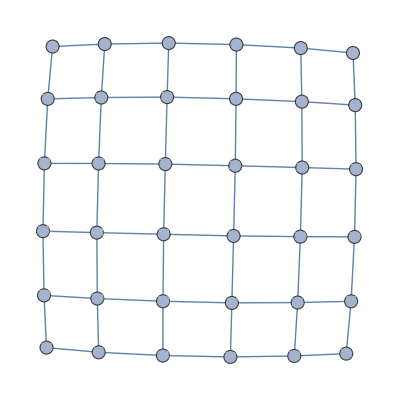

```mathematica
squareGraph[n_Integer]:=
Graph[Flatten[{Table[Table[i*n+j<-> i*n+j+1, {j, 1, n-1}], {i, 0, n-1}], Table[Table[i*n+j<-> i*n+j+n, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.25, EdgeWeight->{_->1}];
(*squareGraph[n_Integer]:=
Graph[Flatten[{Table[Table[{i*n+j-> i*n+j+1, i*n+j+1-> i*n+j}, {j, 1, n-1}], {i, 0, n-1}], Table[Table[{i*n+j-> i*n+j+n, i*n+j+n-> i*n+j}, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.75];*)

myGraph = squareGraph[6]
```

```mathematica
ResourceFunction["DepthFirstSearch"][myGraph,1,3]
```

{}

{}

{}

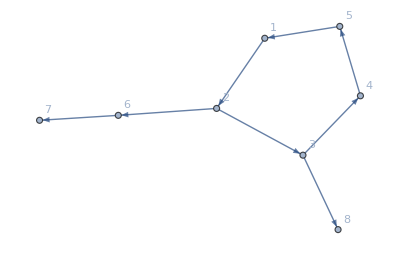

```mathematica
(*Create an undirected cyclic graph*)graph=Graph[{1->2,2->3,3->4,4->5,2->6,6->7,3->8,5->1},VertexLabels->"Name"];

(*Perform a depth-first search starting from node 1 with a maximum depth of 3*)
result=ResourceFunction["DepthFirstSearch"][graph,1,3]

(*Output the result*)
result

(*Highlight the depth-first search path on the graph*)
HighlightGraph[graph,PathGraph[result]]
```

```mathematica
boston = GeoGraphics[GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4521}}]]
```

```mathematica
atlanta = GeoGraphics[GeoBoundsRegion[{{33.7500,33.7900},{-84.4543, -84.4100}}]]
```

```mathematica
osmAtlanta=ResourceFunction["OSMImport"][GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4521}}]]
```

```mathematica
atlanta = GeoGraphics[GeoBoundsRegion[{{33.7500,33.7900},{-84.4543, -84.4100}}]]
```

-Graphics-

```mathematica
osmAtlanta=ResourceFunction["OSMImport"][GeoBoundsRegion[{{33.7500,33.7900},{-84.4543, -84.4100}}]]
```

XML`Parser`XMLGet::prserr: Invalid document structure at Line: 1 Character: 1 in C:\Users\isaia\AppData\Local\Temp\m-0652c160-6efd-4179-8836-5156bc5d92db\map.

Import::fmterr: Cannot import data as XML format.

Part::partw: Part 1 of {} does not exist.

<|Nodes→<||>,Ways→<||>|>

```mathematica
findLengthKPath[k_Integer, st_Integer]:=
Module[{rando := RandomSample[Range[36]]},
candidatePaths = Table[FindPath[myGraph, st, rando[[i]], {k}], {i, 1, 36}];
Select[candidatePaths, Length[#]>0&, 1]
]
```

{1,2,3,4,5,6,12,11,10,9,15}

```mathematica
Head[foundPath]
```

List

{1,2,3,4,5,11,10,9,8,7,13}

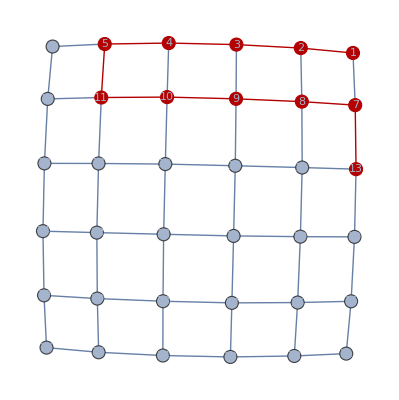

```mathematica
foundPath = Flatten[findLengthKPath[10, 1]]
HighlightGraph[myGraph, PathGraph[foundPath]]
```